Metody numeryczne, Informatyka NS sem. III, 2023/2024

# Projekt 5 – całkowanie numeryczne

Napisz program, który dla argumentów wejściowych:

f – całkowana funkcja,

a – początek przedziału całkowania,

b – koniec przedziału całkowania,

n – liczba punktów węzłowych,

s – sposób wyboru punktów wewnętrznych w podprzedziałach,

poszukiwał będzie przybliżonej wartości całki: ∫_a^b f(x)ⅆx. Całka wyznaczana będzie metodą prostokątów. Po równomiernym podziale przedziału [a,b] przy pomocy n punktów (pierwszy to x=a, ostatni: x=b) program wybierał będzie punkty wewnętrzne (n-1) podprzedziałów w zależności od wartości s, a dokładniej, jeśli:

s=1 – będą to lewe końce podprzedziałów,

s=2 – będą to lewe końce podprzedziałów,

s=3 – będą to środki podprzedziałów,

s=4 – w każdym z podprzedziałów punkt będzie losowany.

Program zwracał będzie wartość dokładną całki (za taką uznajemy wartość wyznaczoną przez \[MathematicaIcon]) i wartość przybliżoną (wyznaczoną metodą prostokątów).
Program nie musi przedstawiać graficznej interpretacji zadania.

## Przykłady

### Przykład 1.

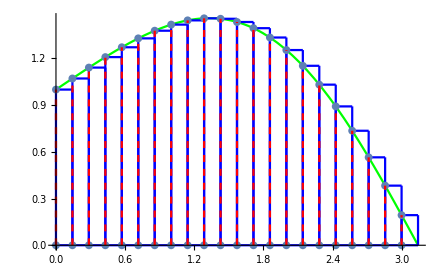
f[x_]:=Cos[x/2]E^Sin[x/2];
całka[f,0,π,23,1]
Całka dokładnie:3.43656
Całka numerycznie:3.5048
-Graphics-

### Przykład 2.

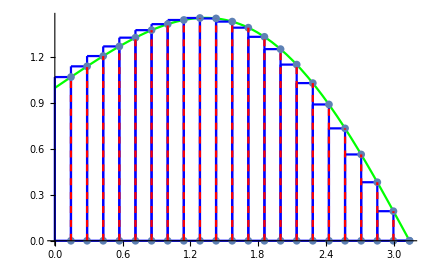
f[x_]:=Cos[x/2]E^Sin[x/2];
całka[f,0,π,23,2]
Całka dokładnie:3.43656
Całka numerycznie:3.362
-Graphics-

### Przykład 3.

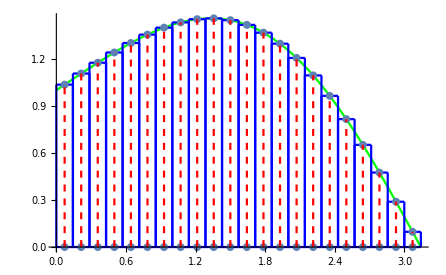
f[x_]:=Cos[x/2]E^Sin[x/2];
całka[f,0,π,23,3]
Całka dokładnie:3.43656
Całka numerycznie:3.43814
-Graphics-

### Przykład 4.

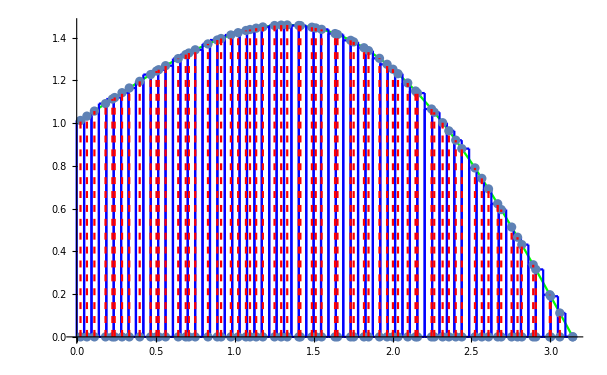
f[x_]:=Cos[x/2]E^Sin[x/2];
całka[f,0,π,68,4]
Całka dokładnie:3.43656
Całka numerycznie:3.43607
-Graphics-